```mathematica
(* calc prin_corr_t09_state0_reordered.jack > data.data *)
(* timeslice_covariance prin_corr_t09_state0_reordered.jack 0 33 > tmp *)
(* head -37 tmp | tail -34 | sed 's/\[//g' | sed 's/\]//g' > data.corr *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/dudek/Research/Lattice/lattice_basics/correlated_fitter

## data & corr

```mathematica
tmp = Import["data.data", "Table"];
data = Table[ {tmp[[i,1]], tmp[[i,2]], tmp[[i,3]]},{i,1,Length[tmp]}]
```

{{0,1,0},{1,7.66217,0.0248621},{2,5.45916,0.0168098},{3,6.01254,0.0463025},{4,3.62732,0.0273218},{5,2.57085,0.0167971},{6,1.97651,0.010937},{7,1.56093,0.00688453},{8,1.24908,0.00413231},{9,1,0},{10,0.806414,0.00229629},{11,0.652801,0.00297699},{12,0.533806,0.0250557},{13,0.428517,0.0024688},{14,0.342489,0.014954},{15,0.282029,0.013514},{16,0.22765,0.00313347},{17,0.184513,0.0017927},{18,0.150743,0.0022952},{19,0.122663,0.0017844},{20,0.103823,0.00471594},{21,0.0802235,0.000826057},{22,0.0651036,0.000695613},{23,0.0527517,0.000731989},{24,0.043109,0.000700149},{25,0.0355678,0.000659365},{26,0.0285623,0.000444374},{27,0.0236746,0.000963856},{28,0.0185675,0.000605231},{29,0.015306,0.000325361},{30,0.0119795,0.000476614},{31,0.00935722,0.00162546},{32,0.00828734,0.000337372},{33,0.00653736,0.000258093}}

```mathematica
corr=Import["data.corr"];
```

```mathematica
(* cut down to size *)
range = Join[Range[6,9], Range[11,34]];(* exclude t<5 & t0=9 *)
Table[ data[[i,1]],{i,range}]
```

{5,6,7,8,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33}

```mathematica
dat = Table[ data[[i]], {i, range}]
```

{{5,2.57085,0.0167971},{6,1.97651,0.010937},{7,1.56093,0.00688453},{8,1.24908,0.00413231},{10,0.806414,0.00229629},{11,0.652801,0.00297699},{12,0.533806,0.0250557},{13,0.428517,0.0024688},{14,0.342489,0.014954},{15,0.282029,0.013514},{16,0.22765,0.00313347},{17,0.184513,0.0017927},{18,0.150743,0.0022952},{19,0.122663,0.0017844},{20,0.103823,0.00471594},{21,0.0802235,0.000826057},{22,0.0651036,0.000695613},{23,0.0527517,0.000731989},{24,0.043109,0.000700149},{25,0.0355678,0.000659365},{26,0.0285623,0.000444374},{27,0.0236746,0.000963856},{28,0.0185675,0.000605231},{29,0.015306,0.000325361},{30,0.0119795,0.000476614},{31,0.00935722,0.00162546},{32,0.00828734,0.000337372},{33,0.00653736,0.000258093}}

```mathematica
cov = Table[ data[[i,3]] corr[[i,j]] data[[j,3]],{i,range}, {j,range}];
invcov = Inverse[cov];
```

```mathematica
Table[Sqrt[cov[[i,i]]],{i,1,Length[dat]}]
```

{0.0167971,0.010937,0.00688453,0.00413231,0.00229629,0.00297699,0.0250557,0.0024688,0.014954,0.013514,0.00313347,0.0017927,0.0022952,0.0017844,0.00471594,0.000826057,0.000695613,0.000731989,0.000700149,0.000659365,0.000444374,0.000963856,0.000605231,0.000325361,0.000476614,0.00162546,0.000337372,0.000258093}

## correlated fit

```mathematica
(* twoExp tmin=5 tmax=33|0.371|0.998|9.133e+06|m=0.2091+/-0.0006,m'=0.840+/-0.074,A=0.010+/-0.003 *)
```

```mathematica
fn[{m_, A_, mm_}, t_] := (1 - A) Exp[ - m(t- 9)] + A Exp[ - mm(t-9)]
```

```mathematica
chisq[{m_, A_, mm_}]:= Sum[ 
(dat[[it,2]] -  fn[{m,A,mm}, dat[[it,1]]]) 
invcov[[it,jt]]  
(dat[[jt,2]] - fn[{m,A,mm}, dat[[jt,1]]] )
, {it,1, Length[dat]}, {jt,1, Length[dat]}]
```

```mathematica
min =FindMinimum[chisq[{m, A, mm}], {{m,0.19}, {A,0.05}, {mm, 1.0}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{9.27301,{m→0.209061,A→0.01004,mm→0.839736}}

```mathematica
min[[1]] / (Length[dat] -3)
```

0.37092

```mathematica
(* BEST FIT uses 2 exponentials
chisq/ndof=9.3/25=0.37
twoExp tmin=5 tmax=33
m0=0.2091+/-0.0006166
m1=0.8397+/-0.07952
A=0.01004+/-0.003692 *)
```

```mathematica
alpha = 1/2({{D[chisq[ {m, A, mm}], {m,2}], D[chisq[ {m, A, mm}], m,A], D[chisq[ {m, A, mm}], m,mm]}, {D[chisq[ {m, A, mm}], m,A], D[chisq[ {m, A, mm}], {A,2}], D[chisq[ {m, A, mm}], A,mm]}, {D[chisq[ {m, A, mm}], m,mm], D[chisq[ {m, A, mm}], A,mm], D[chisq[ {m, A, mm}], {mm,2}]}}) /. min[[2]]
```

{{5.5469×10^6,2.36926×10^6,82559.7},{2.36926×10^6,4.09456×10^6,176653.},{82559.7,176653.,7900.76}}

```mathematica
paramcov = Inverse[alpha]
```

{{3.58063×10^-7,-1.29414×10^-6,0.000025194},{-1.29414×10^-6,0.0000115839,-0.000245482},{0.000025194,-0.000245482,0.00535202}}

```mathematica
Sqrt[paramcov[[1,1]]] (* δm *)
Sqrt[paramcov[[2,2]]] (* δA *)
Sqrt[paramcov[[3,3]]] (* δmm *)
```

0.000598384

0.00340352

0.0731575

```mathematica
(paramcorr = Table[ paramcov[[i,j]]/Sqrt[ paramcov[[i,i]] paramcov[[j,j]] ],{i,1,3}, {j,1,3}] )//TableForm
```

1. | -0.635437 | 0.575517
-0.635437 | 1. | -0.985898
0.575517 | -0.985898 | 1.

```mathematica
(* ensbc' tmp=cat(prin_corr_t09_state0_reordered.jack_prin_corr_exp_fit_mass0.jack,prin_corr_t09_state0_reordered.jack_prin_corr_exp_fit_A.jack)'
ensbc' tmp2=cat(tmp,prin_corr_t09_state0_reordered.jack_prin_corr_exp_fit_mass1.jack)' 

timeslice_covariance tmp2 0 2
read file:tmp2
bins=553
normalised data covariance=
[[1-0.660948 0.607065]
[-0.660948 1-0.987878]
[0.607065-0.987878 1]]
*)
```

```mathematica
dfndm = D[ fn[{m, A, mm}, t], m];
dfndA= D[ fn[{m, A, mm}, t], A];
dfndmm = D[ fn[{m, A, mm}, t], mm];
dfd = {dfndm, dfndA, dfndmm}
```

{(1-A) ⅇ^(-m (-9+t)) (9-t),-ⅇ^(-m (-9+t))+ⅇ^(-mm (-9+t)),A ⅇ^(-mm (-9+t)) (9-t)}

```mathematica
δfn= Sqrt[ dfd.paramcov.dfd ] /. min[[2]]
```

√((ⅇ^(-0.839736 (-9+t))-ⅇ^(-0.209061 (-9+t))) (0.0000115839 (ⅇ^(-0.839736 (-9+t))-ⅇ^(-0.209061 (-9+t)))-2.46463×10^-6 ⅇ^(-0.839736 (-9+t)) (9-t)-1.28114×10^-6 ⅇ^(-0.209061 (-9+t)) (9-t))+0.98996 ⅇ^(-0.209061 (-9+t)) (-1.29414×10^-6 (ⅇ^(-0.839736 (-9+t))-ⅇ^(-0.209061 (-9+t)))+2.52947×10^-7 ⅇ^(-0.839736 (-9+t)) (9-t)+3.54468×10^-7 ⅇ^(-0.209061 (-9+t)) (9-t)) (9-t)+0.01004 ⅇ^(-0.839736 (-9+t)) (-0.000245482 (ⅇ^(-0.839736 (-9+t))-ⅇ^(-0.209061 (-9+t)))+0.0000537342 ⅇ^(-0.839736 (-9+t)) (9-t)+0.000024941 ⅇ^(-0.209061 (-9+t)) (9-t)) (9-t))

```mathematica
fnmin=fn[{m, A, mm}, t]/. min[[2]]
```

0.01004 ⅇ^(-0.839736 (-9+t))+0.98996 ⅇ^(-0.209061 (-9+t))

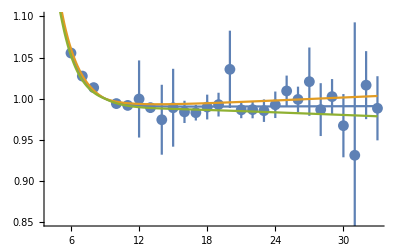

```mathematica
Needs["ErrorBarPlots`"];
daterr = Table[{  {dat[[i,1]], Exp[0.2091 (dat[[i,1]]-9)]dat[[i,2]]}, ErrorBar[Exp[0.2091 (dat[[i,1]]-9)]dat[[i,3]]]}, {i,1,Length[dat]}];
pdat = ErrorListPlot[daterr];
pfit=Plot[{Exp[0.2091 (t-9)](fnmin ),Exp[0.2091 (t-9)](fnmin + δfn), Exp[0.2091 (t-9)](fnmin - δfn)}, {t,0,33}];
Show[pdat,pfit, PlotRange->{.85,1.1}]
```